# QEA - Attitude Control - B-set 2

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

```mathematica
b=2
```

2

```mathematica
b'
```

0&

```mathematica
b:=b
```

```mathematica
b'
```

b'

```mathematica
Solve[m Derivative[Derivative[x]]==-T Cos[θ]&&m Derivative[Derivative[y]]==T Sin[θ]-m g&&x Derivative[Derivative[x]]+y Derivative[Derivative[y]]==-Derivative[x]-Derivative[y],{Derivative[Derivative[x]],Derivative[Derivative[y]],T}]
```

## Basic Pendulum

```mathematica
With[{context="basicpendulum`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{m=1,g=9.8,l=1},initialConditions={θ[0]==π/2,θ'[0]==0};
de={θ''[t]==-m g Sin[θ[t]]/l};
sol=NDSolveValue[Join[initialConditions,de],θ[t],{t,0,10}]
]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

### Animation of pendulum

```mathematica
Animate[ParametricPlot[{Sin[sol],-Cos[sol]},{t,n,n+.1},PlotRange->{{-1,1},{-1,1}}],{n,0,9.9}]
```

### Plot of the path the pendulum covers starting with initial conditions θ[0]=π/2 and θ’[0]=0

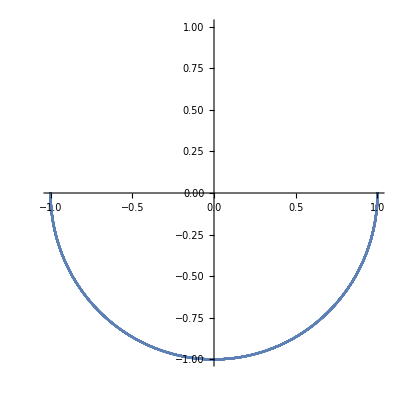

```mathematica
ParametricPlot[{Sin[sol],-Cos[sol]},{t,0,10},PlotRange->{{-1,1},{-1,1}}]
```

### Plot of θ over time with initial conditions θ[0]=π/2 and θ’[0]=0

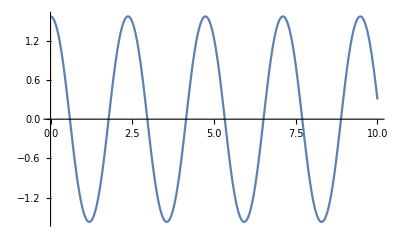

```mathematica
Plot[sol,{t,0,10}]
```

```mathematica
With[{context="basicpendulum`"},If[Context[]==context,End[],"Not in context"]]
```

basicpendulum`